```mathematica
vel:=1
lado:=1
theta:=Pi/3
pos:={lado/3,lado/2.5}
mode[A_,B_,m_,n_,t_,xpos_,ypos_]:=(A*Cos[vel*Pi*Sqrt[m*m+n*n]*t/lado]+B*Sin[vel*Pi*Sqrt[m*m+n*n]*t/lado])Sin[m*Pi*xpos/lado]*Sin[n*Pi*ypos/lado]
wave[t_,xpos_,ypos_]:=mode[0.1,0.1,1,1,t,xpos,ypos]+mode[0.1,0.1,2,2,t,xpos,ypos]+mode[0.1,0.1,4,4,t,xpos,ypos]e
```

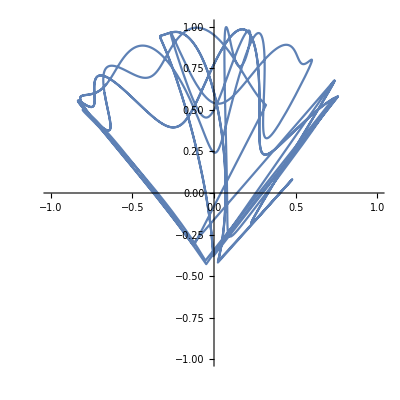

```mathematica
ParametricPlot[{x[alpha[t],beta[t],theta],y[alpha[t],beta[t],theta]},{t,0,2},PlotRange->{{-1,1},{-1,1}},AspectRatio->Full]
```